Based on Optimal_Forager.wxm from Theoretical Ecology class

```mathematica
tw:=1/Integrate[a*2π*r,{r,0,rc}];
```

```mathematica
tw
```

1/(a π rc^2)

```mathematica
tp:=Integrate[2*r/v*a*2π*r,{r,0,rc}]/Integrate[a*2π*r,{r,0,rc}];
```

```mathematica
tp
```

(4 rc)/(3 v)

```mathematica
ti:=tw+tp
```

```mathematica
ei:=e-ew*tw-ep*tp
```

```mathematica
et:=ei/ti
```

```mathematica
et
```

(e-ew/(a π rc^2)-(4 ep rc)/(3 v))/(1/(a π rc^2)+(4 rc)/(3 v))

```mathematica
cond={ew->0.1,ep->1,v->0.5,a->0.005,e->10}
```

{ew→0.1,ep→1,v→0.5,a→0.005,e→10}

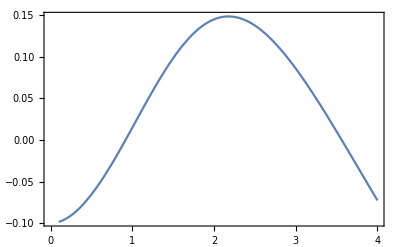

```mathematica
Plot[et/.cond,{rc,0.1,4}]
```

```mathematica
rcopt=Solve[D[et,rc]==0,rc]
```

{{rc→0},{rc→(36 2^(1/3) (ep-ew))/((-69984 a^2 e^3 π^2 v+√(8707129344 a^3 e^3 (ep-ew)^3 π^3+4897760256 a^4 e^6 π^4 v^2))^(1/3))-((-69984 a^2 e^3 π^2 v+√(8707129344 a^3 e^3 (ep-ew)^3 π^3+4897760256 a^4 e^6 π^4 v^2))^(1/3))/(36 2^(1/3) a e π)},{rc→-(18 2^(1/3) (1+ⅈ √3) (ep-ew))/((-69984 a^2 e^3 π^2 v+√(8707129344 a^3 e^3 (ep-ew)^3 π^3+4897760256 a^4 e^6 π^4 v^2))^(1/3))+((1-ⅈ √3) (-69984 a^2 e^3 π^2 v+√(8707129344 a^3 e^3 (ep-ew)^3 π^3+4897760256 a^4 e^6 π^4 v^2))^(1/3))/(72 2^(1/3) a e π)},{rc→-(18 2^(1/3) (1-ⅈ √3) (ep-ew))/((-69984 a^2 e^3 π^2 v+√(8707129344 a^3 e^3 (ep-ew)^3 π^3+4897760256 a^4 e^6 π^4 v^2))^(1/3))+((1+ⅈ √3) (-69984 a^2 e^3 π^2 v+√(8707129344 a^3 e^3 (ep-ew)^3 π^3+4897760256 a^4 e^6 π^4 v^2))^(1/3))/(72 2^(1/3) a e π)}}

```mathematica
FullSimplify[rcopt]
```

{{rc→0},{rc→(2 2^(1/3) a e (ep-ew)-(-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(2/3))/(2^(2/3) a e √π (-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(1/3))},{rc→(4 (-2)^(1/3) a e (-ep+ew)+(1-ⅈ √3) (-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(2/3))/(2 2^(2/3) a e √π (-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(1/3))},{rc→(4 (-2)^(2/3) a e (ep-ew)+2^(1/3) (1+ⅈ √3) (-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(2/3))/(4 a e √π (-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(1/3))}}

```mathematica
rcopt/.cond
```

{{rc→0},{rc→2.17729},{rc→-1.08864-4.55458 ⅈ},{rc→-1.08864+4.55458 ⅈ}}

```mathematica
Plot[(2 2^(1/3) a e (ep-ew)-(-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(2/3))/(2^(2/3) a e √π (-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(1/3))/.{ew->0.1,ep->1,v->0.5,e->10},{a,0,.1}]
```

```mathematica
(2 2^(1/3) a e (ep-ew)-(-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(2/3))/(2^(2/3) a e √π (-3 a^2 e^3 √π v+√(a^3 e^3 (16 (ep-ew)^3+9 a e^3 π v^2)))^(1/3))/.ep->ew
```

-((-3 a^2 e^3 √π v+3 √π √(a^4 e^6 v^2))^(1/3))/(2^(2/3) a e √π)

```mathematica
Solve[H-c*2d*H/a==0,d]
```

{{d→a/(2 c)}}

```mathematica
Solve[H-c*2d*H^2/a==0,d]
```

{{d→a/(2 c H)}}

```mathematica
Solve[H-c*2d*H^1.5/a==0,d]
```

{{d→(0.5 a)/(c H^0.5)}}

```mathematica
Solve[H-c*2d*H^2==0,d]
```

{{d→1/(2 c H)}}

```mathematica
Solve[Sqrt[H]-c*2d H==0,d]
```

{{d→1/(2 c √H)}}

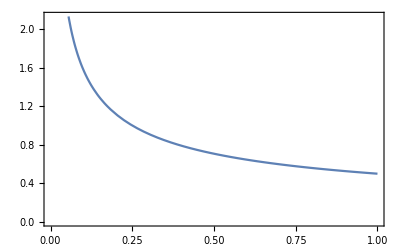

```mathematica
Plot[1/(2 c √H)/.c->1,{H,0.001,1}]
```

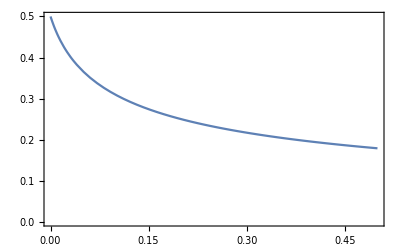

```mathematica
Plot[(-.5+Sqrt[.25+10H])/(2 c H)/.c->10,{H,0,.5}]
```

```mathematica
ropt=(-ep+√(2 e^2 α v+(ep-ew)^2)+ew)/(e α)/.{ew->0.1,ep->1,v->0.5,e->10}
```

(-0.9+√(0.81+100. α))/(10 α)

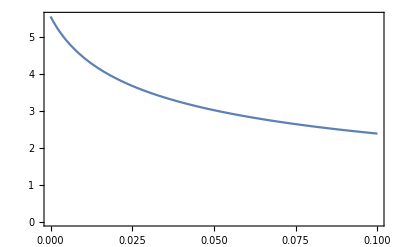

```mathematica
Plxot[ropt,{α,0,0.1}]
```